```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/428fstep4.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

80

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata[[4]]=Take[rawdata,All,2];
```

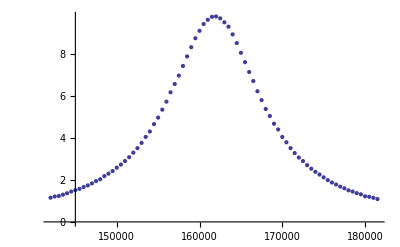

```mathematica
dataplot=ListPlot[plotdata[[4]]]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[4]][[i]]],{max}=freq[[i]]}],{i,1,num}]
```

41{162000.,9.763}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[plotdata,model,{x0,g,b},x,MaxIterations->1000]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.87989×10^-17, -6.97437×10^-13, -6.97437×10^-13}, {0., « 1 », -« 24 »}, {0., 0., -« 24 »}} may contain significant numerical errors.

{BestFitParameters→{x0→6.33488×10^6,g→83.1942,b→83.1942},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 6.33488×10^6 | 1.96056×10^22 | {-3.90398×10^22,3.90398×10^22}
g | 83.1942 | 1.74862×10^25 | {-3.48194×10^25,3.48194×10^25}
b | 83.1942 | 1.74862×10^25 | {-3.48194×10^25,3.48194×10^25},EstimatedVariance→26.475,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 3.88061×10^-8 | 1.29354×10^-8
Error | 77 | 2038.58 | 26.475
Uncorrected Total | 80 | 2038.58 | 
Corrected Total | 79 | 630.522 | ,AsymptoticCorrelationMatrix→(1. | -1. | 1.
-1. | 1. | -1.
1. | -1. | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 3.88206×10^21
Max Parameter-Effects | 1.54305×10^37
95. % Confidence Region | 0.605967}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

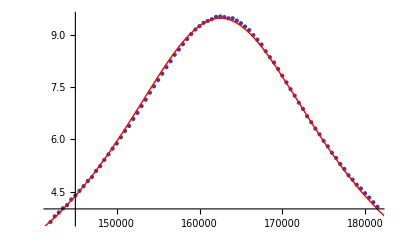

```mathematica
Show[dataplot,fitplot]
```